## 5

```mathematica
Integrate[1/(8 Pi)Exp[-r],{r,Infinity,0}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
∫_∞^0 (∫-Exp[-r]/(8 π)ⅆr)ⅆr
%//N
```

-1/(8 π)

-0.0397887

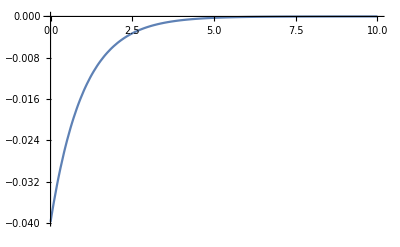

```mathematica
Plot [NIntegrate[1/(8 Pi)Exp[-r],{r,Infinity,x}],{x,0,10},PlotRange->All]
```

### Substitution

```mathematica
D[x/(x-1)^2,x]//Simplify
```

-(1+x)/(-1+x)^3

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
Limit[x/(x-1)^2,{x->1}]
```

∞

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,a}]
```

ConditionalExpression[(-1+ⅇ^(-a/(-1+a)^2))/(8 π), Re[a]≤1||a∉ℝ]

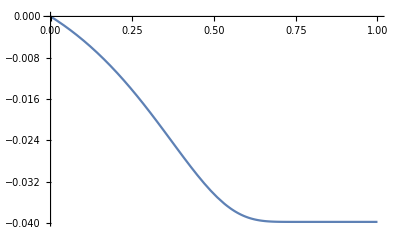

```mathematica
Plot[(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1}]
```

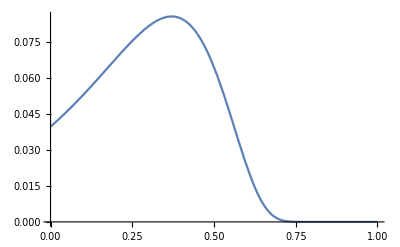

```mathematica
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotRange->All]
```

120208

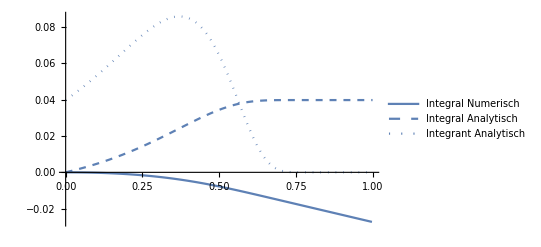

```mathematica
SetDirectory[NotebookDirectory[]];

PrintTemporary["make"];
Run["make"];

PrintTemporary["plot"];
d= Import["poisson2.dat"];
ByteCount[d]

Show[
{
ListLinePlot[{d[[All,{1,2}]]},PlotLegends->{"Integral Numerisch", "ρ"}],
Plot[-(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1},PlotStyle->Dashed,PlotLegends->{"Integral Analytisch"}],
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotStyle->Dotted,
PlotLegends->{"Integrant Analytisch"}]
},
PlotRange->All
]

Export["img/poisson2.pdf",%];
```

96192

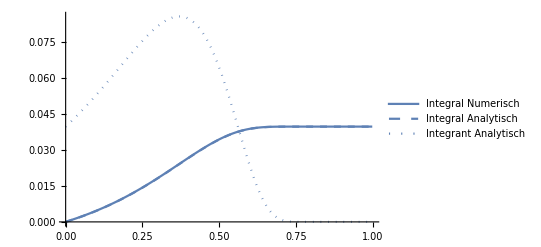

```mathematica
SetDirectory[NotebookDirectory[]];

PrintTemporary["make"];
Run["make"];

PrintTemporary["plot"];
d= Import["summation.dat"];
ByteCount[d]

Show[
{
ListLinePlot[{d[[All,{1,2}]]},PlotLegends->{"Integral Numerisch", "ρ"}],
Plot[-(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1},PlotStyle->Dashed,PlotLegends->{"Integral Analytisch"}],
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotStyle->Dotted,
PlotLegends->{"Integrant Analytisch"}]
},
PlotRange->All
]

Export["img/summation.pdf",%];
```

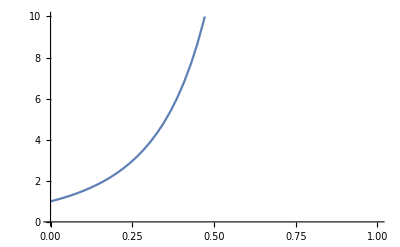

```mathematica
Plot[-(1+x)/(x-1)^3,{x,0,1},PlotRange->{0,10}]
```